```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 40000; 
lowerScore = 20000;
upperScore = 80000; 
targetScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 100;
runningScore = origBaseScore; 

While [iterator < countOuter , 

While [ innerIter < countInner ,
			myRandom = RandomInteger[5];
			If [ myRandom == 0  ∨myRandom == 1 ∨ myRandom == 2 ,(* equal probability of increasing or decreasing score *) 
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
	If[runningScore ≥  origUpperScore ∨  runningScore ≤  origLowerScore,
	runningScore = 0;
	Break[]
	];

	innerIter++;	
	];
If [ runningScore ≠ 0,
	AppendTo[results, (runningScore-origBaseScore)];
];
runningScore = origBaseScore;
innerIter = 0; 
iterator++; 
	];

results
```

{-500,-600,0,500,-200,300,-200,-200,-100,0,200,-500,500,-300,300,-600,600,100,-300,-300,-200,900,-400,300,100,-100,200,0,200,0,200,600,400,-400,-300,-300,100,-1000,-400,200,200,500,400,-1100,600,-300,0,-200,200,200,100,0,-200,400,200,-200,-600,200,-200,100,-500,-200,100,800,300,700,500,600,900,800,-300,-400,300,-500,200,-300,-200,0,100,-700,300,600,600,100,-800,0,0,-100,0,300,-600,500,-400,400,200,-200,300,700,100,700}

```mathematica
number = 10000; 
endLocation = -3000;
expectedData = List[]; 

probabilityEquation = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 4/6)^((number+endLocation)/2)*( 2/6)^((number-endLocation)/2)//N

iterator = 0; 
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[1000,p],k],{p,{0.5}}],{k,800},PlotRange->All,PlotMarkers->Automatic];
```

1.37997525524892×10^-908

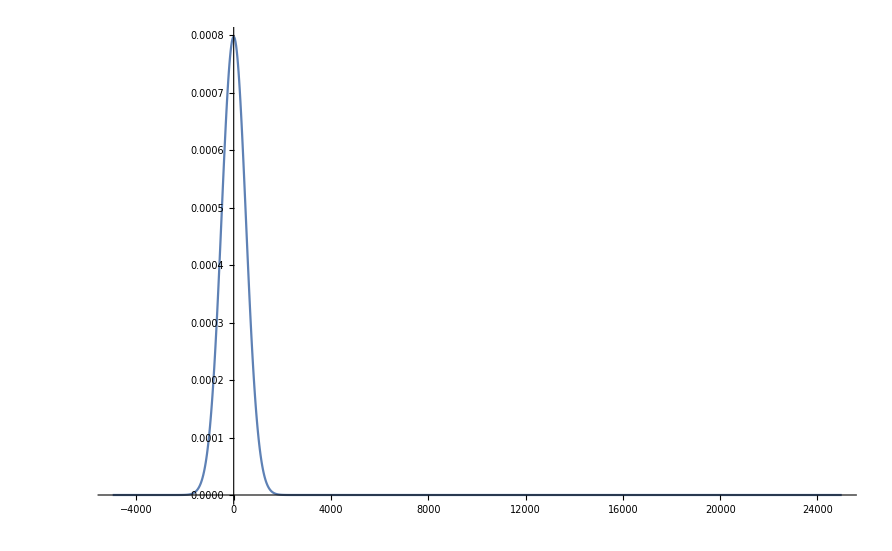

```mathematica
expectedData = List[]; 
iterator = 0;
endLocation = -1000;
number = 10000;
While [endLocation < 5000,
		endLocation = endLocation +scorePerThrow/10;
			
		probabilityValue = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 3/6)^((number+endLocation)/2)*( 3/6)^((number-endLocation)/2)/10;
		AppendTo[expectedData, {(endLocation*5),probabilityValue}];
		iterator++;
	]
expectedData;
```

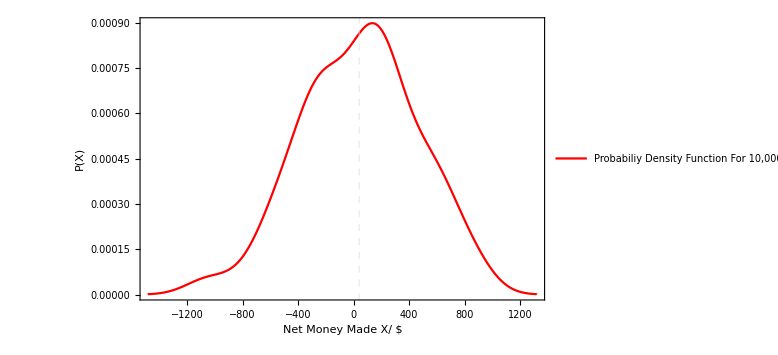

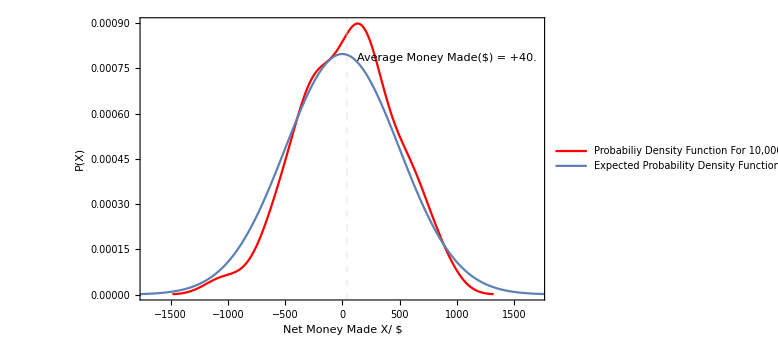

```mathematica
p2 = ListPlot[expectedData, PlotRange->All, Joined -> True,LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotLegends-> {"Expected Probability Density Function Using Binomial Distribution"}];

dataHistogram = SmoothHistogram[results, GridLines-> { {Mean[results]}}, GridLinesStyle-> Dashed,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made X/ $","P(X)","Conditions= 
Starting Money = $40000; 
Money gained per each correct throw = $50;
FAIR dye i.e. P(WIN) = 3/6, P(LOSS) = 3/6
",""}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+Mean[results] //N}},Alignment->{{Left}}],Background->White],{1700,0.0008},{Right,Top}] ,  PlotLegends->{"Probabiliy Density Function For 10,000 Trials"},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
p2;
Show[{dataHistogram,p2} , PlotRange -> {{-1700,1700},{0,0.00090}}]
```